# Transformations affines, fonctions itérées, fractales

## Transformations affines

Une transformation affine T est la composition d’une transformation linéaire L et d’une translation par un vecteur t.  On peut représenter L par une matrice 
L=(l_xx | l_xy
l_yx | l_yy)
et t par un vecteur t = (t_x,t_y); Alors,
T(x
y)=(l_xx | l_xy
l_yx | l_yy)(x
y)+(t_x
t_y)

Il suffit de connaître les images q_1,q_2,q_3 de trois points p_1, p_2, p_3 par la transformation T pour pouvoir la caractériser complètement, en résolvant le système d’équations
Piecewise[{{T(p_i)=q_i, i=1, 2, 3}}]
pour les inconnues L et t (il y a six coefficients en tout, et  six équations).
Cette méthode donne une unique solution lorsque les points p_i sont non-alignés.

```mathematica
(* On trouve une transformation affine à partir de trois points et trois images *)
TrouverTransformationAffine[p_List, q_List]:=Module[{L, lxx, lxy, lyx, lyy,t, tx, ty,sol},
(* On organise nos inconnues *)
L:={{lxx, lxy}, {lyx, lyy}};
t:={tx, ty};

(* On utilise la fonction Solve pour résoudre notre système d'équations *)
sol=Solve[
Table[L.p[[i]]+t==q[[i]],{i,1,3}],
Flatten@{L, t} (* Notre liste d'inconnues *)
];

(* On retourne une liste contenant
1. La matrice L;
 2. Le vecteur t *)
Return[{L, t}/.sol[[1]]];
];

(* Cette fonction applique la transformation affine transfo (donnée comme une liste contenant la matrice L et le vecteur t). *)
AppliquerT[transfo_,point_]:=transfo[[1]].point+transfo[[2]];
```

Par exemple, si on a les équations suivantes :
T(0, 0)=(1, 0);  T(1, 1) = (2, -1);  T(0, 2)=(3, 1)

```mathematica
{L, t}=TrouverTransformationAffine[
p={{0, 0},{1, 1}, {0, 2}},
qCible={{1, 0}, {2, -1}, {3, 1}}];
```

Alors on trouve la transformation

```mathematica
MatrixForm/@{L, t}
```

{(0 | 1
-3/2 | 1/2),(1
0)}

On vérifie qu’on a bien la bonne transformation :

```mathematica
q=AppliquerT[{L, t},#]&/@p;
q==qCible
```

True

Voici une représentation visuelle de la transformation :

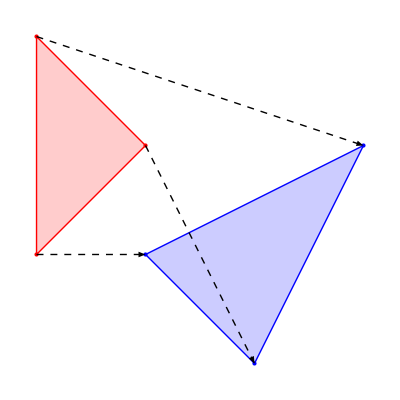

```mathematica
Show[
Graphics[{Red, Line[Append[p, p[[1]]]],Point/@p}],
Graphics[{Red, Opacity[.2],Polygon[p]}],Graphics[{Blue, Line[Append[q, q[[1]]]],Point/@q}],
Graphics[{Blue, Opacity[.2],Polygon[q]}],
Graphics[{Black,Dashed,
Table[Arrow[{p[[i]],q[[i]]}],{i,1,3}]
}]
]
```

## Systèmes de fonctions itérées et fractales

Soit A une région du plan, et soient T_1, T_2, T_3, ..., T_n des transformations affines. On note
W(A) =T_1(A) ∪ T_2(A) ∪ T_3(A) ∪ ... ∪ T_n (A)

La fonction W est une fonction d’ensembles qui, partant de A, crée n copies de A transformées par les transformations affines T_i, i=1, 2, 3, ..., n.

```mathematica
W[transfos_List,A_]:=Join@@
Table[
AppliquerT[transfos[[i]],#]&/@A,
{i,1,Length[transfos]}
];
```

Lorsque W est une contraction (c’est-à-dire que les images de deux points par les T_i sont toujours plus proches que les points de départ), elle possède un point fixe qui satisfait A = W(A). La nature auto-réplicative de A (qui contient plusieurs images de lui-même) fait des fractales.
Les itérés d’un ensemble de départ sous W convergent vers cette fractale.

```mathematica
(* Liste des transformations affines *)
transfos={
{L={{1/2, 0},{0, 1/2}},{0,0}},
{L, {1/4,1/2}},
{L,{1/2, 0}}
};
```

```mathematica
(* Initialisation *)
A={{0., 0.}};
n=0;nmax=10;
```

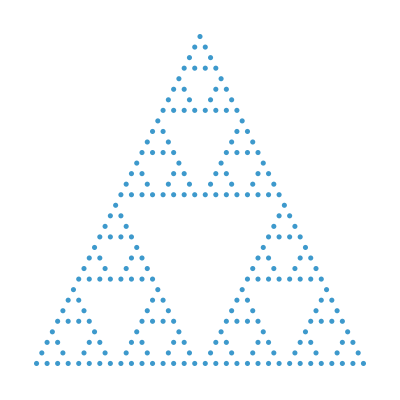

243 points.

0.054436 secondes.

```mathematica
(* On dessine A, puis on calcule la prochaine itération *)
temps1=SessionTime[];

ListPlot[A,AspectRatio->Automatic, PlotRange->All,Axes->False,Joined->False]
Print[Length[A], " point",If[Length[A]>1,"s.","."]];

If[n < nmax,
(* On fait une itération *)
A = W[transfos,A];
n+=1;
]
temps2=SessionTime[];

Print[temps2-temps1, " secondes."];
```

### Le même algorithme, à répétition.

Le morceau de code suivant génère la fractale par itérations comme précédemment, mais en bouclant tout d’un coup. Pour limiter le nombre d’itérations on peut déterminer un maximum à partir du nombre de points qu’on veut

```mathematica
(* La fonction NMax retourne le nombre minimum d'itérations qu'il faut faire pour avoir npoints points avec les transformations transfos *)
NMax[transfos_,npoints_]:=Module[{nt},
nt=Length[transfos];
Return[
If[nt>1,
Ceiling[Log[npoints]/Log[nt]],
npoints
]
]
];
```

```mathematica
(* L'algorithme de dessin de fractale *)
DessinerFractale[transfos_List,nPoints_,init_]:=Module[
{temps1, temps2, A, n, nmax, lp},
temps1=SessionTime[];

A=init;
n=0;

nmax=NMax[transfos, 100000];
Print["nmax = ",nmax];

While[n<nmax,
A=W[transfos,A];
n++;
];

lp=ListPlot[A,AspectRatio->Automatic,Frame->True, Axes->False,PlotRange->All,ImageSize->Medium];

Print[Length[A]," point",If[Length[A]>1,"s.","."]];
temps2=SessionTime[];
Print[temps2-temps1," secondes."];
Return[lp]
];
origine={{0., 0.}};
```

```mathematica
DessinerFractale[transfos,100000,origine]
```

Voici des listes de transformations affines pour quelques fractales :

```mathematica
(* Le triangle de Sierpinski *)
triangleDeSierpinski={
{L={{1/2, 0},{0, 1/2}},{0,0}},
{L, {1/4, √3/4}},
{L,{1/2, 0}}
};
```

```mathematica
DessinerFractale[triangleDeSierpinski,nPoints,origine]
```

```mathematica
(* Tapis de Sierpinski *)
tapisDeSierpinski={
{L={{1/3,0},{0, 1/3}},{0,0}},
{L,{1/3,0}},{L,{2/3,0}},
{L,{0,1/3}},{L,{2/3,1/3}},
{L,{0, 2/3}},{L,{1/3,2/3}},{L,{2/3,2/3}}
};
```

```mathematica
DessinerFractale[tapisDeSierpinski,nPoints,origine]
```

```mathematica
(* La fougère du manuel *)
fougèreDuManuel={
{{{0.85,0.04},{-0.04,0.84}},{0.,1.6}},
{{{0.2,-0.26},{0.23,0.22}},{0., 1.6}},
{{{-0.15,0.28},{0.26, 0.24}},{0.,.53}},
{{{0., 0.},{0., 0.16}},{0., 0.}}
};
```

```mathematica
dessinFougère=DessinerFractale[fougèreDuManuel,nPoints,origine]
```

nmax = 9

262144 points.

2.241738 secondes.

### Un algorithme qui dessine « plus égal »

L’algorithme suivant génère le dessin de la fractale en appliquant des transformations aléatoires au dernier point de la liste de points A. Les probabilités des transformations sont choisies environ proportionnellement à la valeur absolue de leurs déterminants, histoire que les points soient distribués plus équitablement dans le dessin.

Cet algorithme est (à quelques modifications près) ce qui est donné dans le manuel pour tracer la fougère.

```mathematica
(* On calcule des poids pour les transformations affines de la liste transfos *)
PoidsTransfos[transfos_]:=Module[{dets, totalDets},
dets=Table[Abs[Det[transfos[[i,1]]]] ,{i, 1, Length[transfos]}];
totalDets=Total[dets];
dets=(#+.01(totalDets))&/@dets;
Return[dets/Total[dets]]
];
PoidsTransfosEqui[transfos_]:=Array[1&,Length[transfos]]/Length[transfos];
```

```mathematica
(* Algorithme stochastique *)
DessinerFractaleStocha[transfos_,nPoints_,init_]:=Module[
{temps1, temps2, transfoAléatoire,dernierPoint,A, lp},
temps1=SessionTime[];
(* On choisira chaque fois une transfo aléatoire. Le := signifie que le choix aléatoire se fait chaque fois que le symbole est utilisé. *)
transfoAléatoire:=RandomChoice[PoidsTransfos[transfos]->transfos];

dernierPoint=init;
(* Les fonctions Reap et Sow sont beaucoup plus efficaces que AppendTo pour la génération itérative d'une liste *)
A=Reap[
Do[
Sow[
dernierPoint=AppliquerT[transfoAléatoire,dernierPoint]
]
,{nPoints-1}];
][[2]];
A=Join[{init},A[[1]]]; (* La fonction Reap renvoie un format peu pratique. On corrige ça. *)

lp=ListPlot[A,AspectRatio->Automatic,Frame->True, Axes->False,PlotRange->All,ImageSize->Medium];
Print[Length[A]," point",If[Length[A]>1,"s.","."]];
temps2=SessionTime[];
Print[temps2-temps1," secondes."];

Return[lp]
];
```

```mathematica
Grid[
{{"Par les itérés", "Algorithme stochastique"},
{dessinFougère,
DessinerFractaleStocha[fougèreDuManuel, 100000,origine[[1]]]}}]
```

100000 points.

3.858318 secondes.

### Solutions aux exercices du TP 7

Dans ce qui suit, j’ai regroupé des ensembles de transformations affines pour générer les fractales des exercices du TP 7.

```mathematica
(* Matrices utiles *)
R[θ_]:={{Cos[θ], -Sin[θ]},{Sin[θ],Cos[θ]}}; (* Rotation *)
S[r_]:=r IdentityMatrix[2]; (* Mise à l'éche..e *)
S[rx_, ry_]:={{rx, 0},{0, ry}}; (* Étirement anisotrope *)
K[kx_]:={{1, kx}, {0, 1}}; (* Cisaillement *)

(* On fait les dessins avec 100000 points *)
nPoints=100000;
```

Exercice 1 a. Je donne une liste de transformations possibles.

```mathematica
(* 1 a : l'origine est au bas de la tige; l'axe des y est parallèle à la tige.
La tige est de hauteur 1.2; l'arbre au complet est de hauteur 3.1.
Les branches sont contractées de façon anisotrope par des facteurs 2/3 (en y) et 17/30 (en x) *)
exercice1a={
{S[0, 1.2/3.1], {0., 0.}} (* Tige *),
{R[π/4].S[17/30, 2/3], {0., 1.2}} , (* Branche de gauche *)
{R[-π/4].S[17/30, 2/3],{0.,1.2}} (* Branche de droite *)
};
```

```mathematica
DessinerFractale[exercice1a, nPoints,origine]
```

nmax = 11

177147 points.

2.141182 secondes.

```mathematica
(* 1 b : l'origine est au bas à gauche du dessin, dont les côtés longs sont de longueur 1.*)
exercice1b ={
{S[1/2], {0., 0.}},
{S[1/2].R[π/2], {1., 0.}},
{S[1/2].R[-π/2], {0., 1.}}
};
```

```mathematica
dessin1b=DessinerFractale[exercice1b, nPoints,origine]
```

nmax = 11

177147 points.

1.938118 secondes.

```mathematica
(* 1 c : L'origine est au bas à gauche du dessin; les côtés longs sont de longueur 1. *)
exercice1c ={
{S[1/2], {0., 0.}},
{S[1/2], {.5, .0}},
{S[1/2].R[π/2], {1., .5}}
};
```

```mathematica
DessinerFractale[exercice1c, nPoints, origine]
```

nmax = 11

177147 points.

1.909078 secondes.

```mathematica
(* 1 d : L'origine est au centre de la figure; le carré circonscrit est le (carré [-1, 1])^2 *)
exercice1d={
{S[1/3], {0, 0}},
{S[1/2],{-1/2, 1/2}},
{S[1/2].R[π/2],{-1/2, -1/2}},
{S[1/2].R[-π/2],{1/2, 1/2}}
};
```

```mathematica
DessinerFractale[exercice1d,nPoints, origine]
```

nmax = 9

262144 points.

3.186411 secondes.

Exercice 1 b. Une façon triviale de produire un second ensemble de transformations est de simplement donner des transformations qui sont équivalentes à W(W(A)). Par exemple ,  pour la fractale de la figure 11.12 (b) :

```mathematica
(* 1 b, version 2 : *)
exercice1b2={
{S[1/4],{0, 0}},{S[1/4],{0, 1/2}},{S[1/4],{1/2, 0}},
{S[1/4].R[π/2], {1/2, 0}},{S[1/4].R[π/2],{1, 0}},
{S[1/4].R[-π/2],{0, 1/2}},{S[1/4].R[-π/2],{0, 1}},
{S[1/4].R[π], {1, 1/2}},{S[1/4].R[π],{1/2, 1}}
};
```

```mathematica
Grid[
{{"Version 1 (précédente)", "Version 2"},
{dessin1b, dessin1b2=DessinerFractale[exercice1b2,nPoints,origine]}
}
]
```

nmax = 6

531441 points.

5.94611 secondes.

Exercice 2.

```mathematica
(* Exercice 2 a : l'origine est en bas à gauche; le carré circonscrit est de côté 1. *)
exercice2a={
{S[1/2],{0, 0}},
{S[1/2],{1/2, 0}},
{S[1/2, -1/2],{0, 1}}
};
```

```mathematica
dessin2a=DessinerFractale[exercice2a,nPoints,origine]
```

nmax = 11

177147 points.

2.183344 secondes.

```mathematica
(* Exercice 2 b : l'origine est en bas à droite; le carré circonscrit est de côté 1. *)
exercice2b={
{S[1/2],{0, 0}},
{S[1/2], {0, 1/2}},
{S[1/2],{1/2, 0}},
TrouverTransformationAffine[
{{0, 0}, {0, 1}, {1, 0}},
{{3/5, 1/2}, {3/5, 9/10},{1, 1/2}}]
};
```

```mathematica
dessin2b=DessinerFractale[exercice2b,nPoints, origine]
```

nmax = 9

262144 points.

3.148353 secondes.

```mathematica
(* Exercice 2 c : L'origine est au centre de la figure. Si la figure est de hauteur totale 1 (donc de -1/2 à 1/2), alors elle est de longneure l = 1 + l/2, donc l = 2, et il faut translater tout par +±5/4*)
exercice2c={
{S[1/2], {0, 0}},
{S[1/2].R[π/2], {-5/4, 0}},
{S[1/2].R[-π/2], {5/4, 0}}
};
```

```mathematica
dessin2c=DessinerFractale[exercice2c,nPoints,origine]
```

nmax = 11

177147 points.

2.268156 secondes.

```mathematica
(* Exercice 2 d : L'origine est au centre de la figure. Le centre des plus petits hexagones est à distance 1. du centre *)
cotes2d=6;
scale2d=Sin[π/cotes2d]/(1+Sin[π/cotes2d]);
exercice2d=Table[
{S[scale2d].R[2π i/cotes2d], R[2π i/cotes2d].{1, 0}}
,{i,0, cotes2d-1}
];

(* Vous pouvez vous amuser à changer cotes2d pour obtenir d'autres ngones de Sierpinski.*)
```

```mathematica
dessin2d=DessinerFractale[exercice2d,nPoints,origine]
```

nmax = 7

279936 points.

3.642108 secondes.

(On remarque que les bords de cette fractale sont des flocons de von Koch -- voir Exercice 10)

Exercice 3.

```mathematica
(* Exercice 3 a : L'origine est au coin inférieur gauche; le carré circonscrit est de côté 1. *)
exercice3a ={
{S[1/3],{1/3, 0}}, {S[1/3],{0, 1/3}},
{S[1/3],{1/3, 2/3}}, {S[1/3],{2/3, 1/3}}
};
```

```mathematica
dessin3a=DessinerFractale[exercice3a,nPoints,origine]
```

nmax = 9

262144 points.

3.176574 secondes.

```mathematica
(* Exercice 3 b : L'origine est au coin inférieur gauche; le carré circonscrit est de côté 1. *)
exercice3b=triangleDeSierpinski;
```

```mathematica
dessin3b=DessinerFractale[exercice3b,nPoints,origine]
```

nmax = 11

177147 points.

2.389916 secondes.

```mathematica
(* Exercice 3 c : L'origine est au coin inférieur gauche; le carré circonscrit est de côté 1. *)
exercice3c={
{S[2/5],{0, 0}},
{S[2/5],{3/5, 0}},
{S[2/5],{0, 3/5}},
{S[2/5],{3/5, 3/5}}
};
```

```mathematica
dessin3c=DessinerFractale[exercice3c,nPoints,origine]
```

```mathematica
(* Exercice 3 d : L'origine est au coin inférieur gauche;
le carré circonscrit est de côté 1. *)
exercice3d={
{S[1/2, -1/2],{0,√3/4}},
{S[1/2, -1/2],{1/4, √3/2}},
{S[1/2, -1/2],{1/2, √3/4}}
};
```

```mathematica
dessin3d=DessinerFractale[exercice3d,nPoints,origine]
```

Exercice 4.

```mathematica
(* Exercice 4 a : L'origine est en bas au centre; le carré circonscrit est [-1, 1]x[0, 2] *)
exercice4a={
{S[-1/2, 1/2], {-1/2, 0}},
{S[1/2],{1/2, 0}},
{S[1/2].R[π/2], {0,3/2 }}
};
```

```mathematica
dessin4a=DessinerFractale[exercice4a, nPoints,origine]
```

```mathematica
(* Exercice 4 b : L'origine est au sommet du haut; les deux sommets du bas ont les coordonnées (-1/2, -1) et (1/2, -1)*)
exercice4b={
{S[1/2],{0, 0}},
{S[1/2],{-1/4, -1/2}},
{S[1/2],{1/4, -1/2}},
{S[1/4],{0, -1}}
};
```

```mathematica
dessin4b=DessinerFractale[exercice4b,nPoints,origine]
```

Exercice 10 a. On dessine le flocon de von Koch.

```mathematica
floconDeVonKoch={
{S[1/3],{-1/3, 0}},
{S[1/3],{1/3, 0}},
{S[1/3].R[π/3], {-1/12, √3/12}},
{S[1/3].R[-π/3],{1/12, √3/12}}
};
```

```mathematica
dessinVonKoch=DessinerFractale[floconDeVonKoch,nPoints,origine]
```

Exercice 10 b. On remarque que le flocon de von Koch peut être constitué de deux copies de lui-même seulement.

```mathematica
floconDeVonKoch2={
{R[π/6].S[√(1/3), -√(1/3)], {-1/4, √3/12}},
{R[-π/6].S[√(1/3), -√(1/3)],{1/4,√3/12}}
};
```

```mathematica
Grid@Transpose@{
{"Version 1 : ", dessinVonKoch},
{"Version 2 : ", DessinerFractale[floconDeVonKoch2,nPoints,origine]}}
```

## Facteurs de contraction et dimensions fractales

### Facteurs de contraction

Le facteur de contraction d’une transformation affine T est un nombre r tel que pour tous vecteurs x, y, on a que
d(T(x), T(y)) <= r d(x, y);
c’est un facteur de contraction exact lorsque l’on a l’égalité pour tous x, y.

À l’aide d’un peu d’algèbre linéaire, on voit rapidement que si L est la partie linéaire de T,
r = max{ |λ| : λ est une val. propre de L}

```mathematica
(* On définit le facteur de contraction *)
FacteurDeContraction[transfo_]:=
Max@(Abs/@Eigenvalues[transfo[[1]]]);
ContractionExacteQ[transfo_]:=
((Max[#]-Min[#])&@(Abs/@Eigenvalues[transfo[[1]]]))==0;
```

Par exemple, toutes les transformations affines pour le triangle de Sierpinski ont le même facteur de contraction exact :

```mathematica
Column[Map[MatrixForm,triangleDeSierpinski,{2}]]
FacteurDeContraction/@triangleDeSierpinski
```

{(1/2 | 0
0 | 1/2),(0
0)}
{(1/2 | 0
0 | 1/2),(1/4
(√3)/4)}
{(1/2 | 0
0 | 1/2),(1/2
0)}

{1/2,1/2,1/2}

```mathematica
ContractionExacteQ/@triangleDeSierpinski
```

{True,True,True}

Ce n’est pas le cas pour les transformations affines de l’exercice 1 a :

```mathematica
Column[Map[MatrixForm,exercice1a,{2}]]
FacteurDeContraction/@exercice1a
```

{(0 | 0
0 | 0.387097),(0.
0.)}
{(17/(30 √2) | -(√2)/3
17/(30 √2) | (√2)/3),(0.
1.2)}
{(17/(30 √2) | (√2)/3
-17/(30 √2) | (√2)/3),(0.
1.2)}

{0.387097,(√(17/5))/3,(√(17/5))/3}

```mathematica
ContractionExacteQ/@exercice1a
```

{False,True,True}

### Dimension fractale

La dimension fractale d’une région du plan (ou de l’espace) est définie comme
lim_(n->∞) (log N(1/n))/(log n)=dim(A),
où N(1/n) est le nombre de carrés (ou de cubes) de côté 1/n requis pour couvrir la région A.

Si les transformations affines T_i ont toutes des facteurs de contraction exacts r_i, pour i=1, ..., n, alors le point fixe A compact du système de fonctions itérées W=∪_i T_i  a la dimension fractale dim A qui satisfait :
∑_i r_i^(dim A)=1

```mathematica
DimensionFractale[transfos_]:=Module[{r,sol},
If[ContractionExacteQ/@transfos!=Array[True&,Length[transfos]],
Print["Les transformations n'ont pas toutes des facteurs de contraction exacts."];,

(* Si les facteurs de contraction sont tous exacts *)
r=FacteurDeContraction/@transfos;
sol=Solve[Total[r^dim]==1,dim,Reals];
Return[dim/.sol[[1]]];
]];
```

```mathematica
DimensionFractale[triangleDeSierpinski]
```

Log[3]/Log[2]